```mathematica
SetDirectory["/Users/lorenzosperi/Documents/GitHub/testGRwEMRIs/mathematica_notebooks_fluxes_to_Cpp/"]
Get["KerrGeodesics`"]
Needs["ChebInt`"]
```

/Users/lorenzosperi/Documents/GitHub/testGRwEMRIs/mathematica_notebooks_fluxes_to_Cpp

```mathematica
(*Quit*)
```

# Functions

```mathematica
Ωϕ[0,p_,e_]:=Evaluate@Simplify[KerrGeoFrequencies[0,p,e,1]["Ω_ϕ"],{-3-e^2+p>0}]
```

```mathematica
Ωϕcirc[a_,r_]:=1/(a+r^(3/2))
```

```mathematica
Clear[xfromape]
xfromape[a_,p_,_?PossibleZeroQ]:=(Ωϕcirc[a,p])^(2/3)
xfromape[a_?Negative,p_,e_]:=(Abs[KerrGeoFrequencies[-a,p,e,-1]["Ω_ϕ"]])^(2/3)
xfromape[a_,p_,e_]:=Abs[KerrGeoFrequencies[a,p,e,1]["Ω_ϕ"]]^(2/3)
xfromape[a_?PossibleZeroQ,p_,e_]:=(Ωϕ[0,p,e]^(2/3))
```

```mathematica
Clear[pLSO];
pLSO[a_?Negative,e_?PossibleZeroQ]:=pLSO[a,e]=KerrGeoISCO[-a,-1]
pLSO[a_?NumericQ,e_?PossibleZeroQ]:=pLSO[a,e]=KerrGeoISCO[a,1]
pLSO[a_?PossibleZeroQ,e_?NumericQ]:=pLSO[a,e]=KerrGeoSeparatrix[0,e,1]
pLSO[a_Real?Negative,e_?NumericQ]:=pLSO[a,e]=KerrGeoSeparatrix[-a,e,-1]
pLSO[a_?NumericQ,e_?NumericQ]:=pLSO[a,e]=KerrGeoSeparatrix[a,e,1]
```

```mathematica
Clear[xLSO];
xLSO[a_?NumericQ,e_?NumericQ]:=xLSO[a,e]=Ωϕcirc[a,pLSO[a,e]/(1+e)]^(2/3)
```

```mathematica
auefromape[{a_,p_,e_}]:={a,((1+ e)xfromape[a,p,e])/xLSO[a,e],e}
```

check some values

```mathematica
KerrGeoFrequencies[a,p,e,1]["Ω_ϕ"]/.{a->0.7, p->3.72159,e->0.189091}
```

0.13021

```mathematica
pLSO[a,e]/.{a->0.7, p->3.72159,e->0.189091}
```

3.62159

```mathematica
Ωϕcirc[a,pLSO[a,e]/(1+e)]/.{a->0.7, p->3.72159,e->0.189091}
```

0.166244

```mathematica
((1+ e)xfromape[a,p,e])/xLSO[a,e]/.{a->0.7, p->3.72159,e->0.189091}
```

1.01037

# Interpolation

Set precision

```mathematica
prec=24;
amax=SetPrecision[99/100,prec];
umax=SetPrecision[97/100,prec];
umin=SetPrecision[8/100,prec];
emax=SetPrecision[5/10,prec];
```

### xLSO

To interpolate the LSO location, it is better to use an alternative coordinate for the spin .

```mathematica
ϵ==√(1-a^2)
```

ϵ==√(1-a^2)

```mathematica
ϵmin=√(1-amax);
ϵmax=√(1+amax);
```

Generate LSO data .

```mathematica
xLSOtab=Flatten[Table[{ϵ,e,xLSO[1-ϵ^2,e]},{ϵ,ChebyshevNodes[36,ϵmin,ϵmax]},{e,ChebyshevNodes[18,0,emax]}],1];
```

Plot to check data quality .

```mathematica
ListPointPlot3D[xLSOtab]
```

-Graphics3D-

Interpolate

```mathematica
{xLSOintϵ,xLSOinterr,xLSOintcoef}=ChebyshevInterpolate[xLSOtab,{36,ϵmin,ϵmax},{18,0,emax}];
```

Estimated interpolation error

```mathematica
xLSOinterr
```

5.1302×10^-13

Construct interpolant in term of original (a, e) coordinates:

```mathematica
xLSOint=Function[{a,e},Evaluate[N@Chop[xLSOintϵ[√(1-a),e],10^-15]]];
```

```mathematica
CForm[xLSOint[a,e]];
```

Construct interpolant for Maarten’s variable

```mathematica
xfromape[a,p,e]
```

Abs[(p √((1+1)/(1+1))+a 1+1)/(4 √(1-1/p)+1/EllipticK[1])]^(2/3)
 |  |  |  |

## Load data

```mathematica
data=Import["/Users/lorenzosperi/Documents/GitHub/testGRwEMRIs/mathematica_notebooks_fluxes_to_Cpp/scalar_Edot_Ldot/scalar_level2.wdx"];
```

## Interpolate data

### EdotInf

Find (a,u,e) phase space coordinates, and rescale by 5/32 p^5.

```mathematica
(*Edotinftab=Sort[ Flatten[{N@Round[auefromape@#[[1;;3]],10^-10],(#[[2]])^4(#[[5]]+#[[4]])}]&/@data];*)
Edotinftab=Sort[ Flatten[{N@Round[auefromape@#[[1;;3]],10^-10],(#[[5]]+#[[4]])}]&/@data];
(*Ldotinftab=Sort[ Flatten[{N@Round[auefromape@#[[1;;3]],10^-10],(#[[2]])^(5/2)Abs[(#[[7]] +#[[6]] )] }]&/@data];*)
Ldotinftab=Sort[ Flatten[{N@Round[auefromape@#[[1;;3]],10^-10],Abs[(#[[7]] +#[[6]] )] }]&/@data];
```

Check smoothness/dynamical range of data .

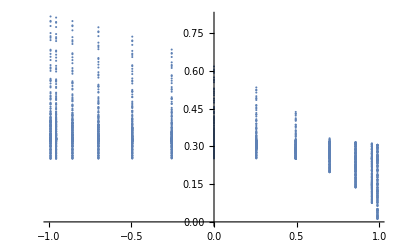

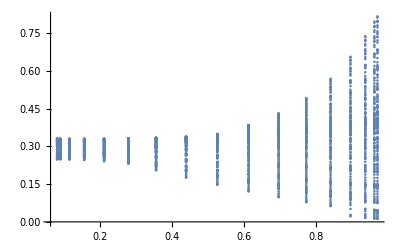

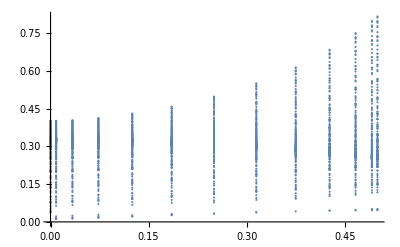

```mathematica
ListPlot[Edotinftab[[All,{1,4}]],PlotRange->All]
ListPlot[Edotinftab[[All,{2,4}]],PlotRange->All]
ListPlot[Edotinftab[[All,{3,4}]],PlotRange->All]
```

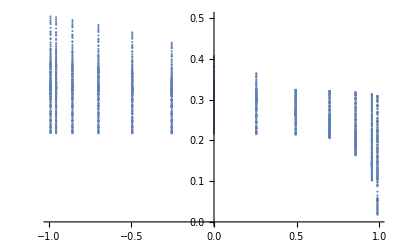

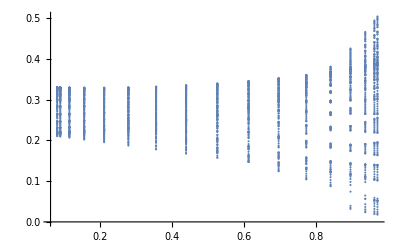

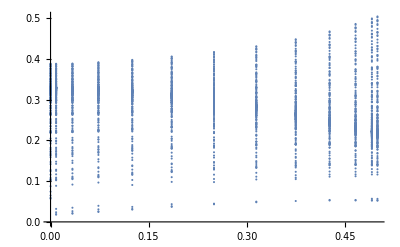

```mathematica
ListPlot[Ldotinftab[[All,{1,4}]],PlotRange->All]
ListPlot[Ldotinftab[[All,{2,4}]],PlotRange->All]
ListPlot[Ldotinftab[[All,{3,4}]],PlotRange->All]
```

Interpolate

```mathematica
{EdotinfIntofaue,EdotinfErr,EdotinfCoef}=ChebyshevInterpolate[Edotinftab, {12,-amax,amax},{16,umin,umax},{12,0,emax},"GL"];
{LdotinfIntofaue,LdotinfErr,LdotinfCoef}=ChebyshevInterpolate[Ldotinftab, {12,-amax,amax},{16,umin,umax},{12,0,emax},"GL"];
```

The estimate error in the interpolant is of order few percent :

```mathematica
EdotinfErr
```

0.0005608803372397575810752880875594

```mathematica
LdotinfErr
```

0.0006731449948945412358086729809291

Construct interpolant in (a, p, e) coordinates and restore overall scaling .

```mathematica
(*EdotMaartenCoord = Function[{a,r,e},1/p^4 EdotinfIntofaue@@{a,r,e}];
LdotMaartenCoord = Function[{a,r,e},1/p^(5/2)LdotinfIntofaue@@{a,r,e}];*)
EdotMaartenCoord = Function[{a,r,e},EdotinfIntofaue@@{a,r,e}];
LdotMaartenCoord = Function[{a,r,e},LdotinfIntofaue@@{a,r,e}];
```

```mathematica
EdotinfErr/EdotMaartenCoord[-0.7,0.08, 0.1]
LdotinfErr/LdotMaartenCoord[-0.7,0.08, 0.1]
```

0.00171571 p^4

0.00207288 p^(5/2)

```mathematica
aa = ChebyshevNodes[32,-amax,amax];
ee = ChebyshevNodes[32,0.0,emax];
rr = ChebyshevNodes[32,umin,umax];
umax
```

0.97

```mathematica
DiscretePlot3D[EdotinfIntofaue[0.987,r,e]/4,{r,rr},{e,ee}]
(*Plot3D[EdotinfIntofaue[0.9,r,e],{r, 0.1,0.8},{e, 0.0, 0.5}]*)
```

-Graphics3D-

# Transform to C expression

```mathematica
(*expression=CForm[((1+e)xfromape[a,p,e])/xLSOint[a,e]];
str=OpenWrite["ratio.hh"];
WriteString[str," double variable = ",expression,";"];
WriteString[str," double variable = ",ExportString[expression,"Text"]];
Close[str];*)
```

Edot expression in terms of Maarten’s coordinate

```mathematica
(*expression=CForm[EdotMaartenCoord[a,r,e]];
str=OpenWrite["output2.hh"];
WriteString[str," double variable = ",expression,";"];
WriteString[str," double variable = ",ExportString[expression,"Text"]];
Close[str];*)
```

```mathematica
(*Experimental`OptimizeExpression[EdotMaartenCoord[a,r,e]];*)
```

```mathematica
OptimizeExpressionToC[expr_]:=Module[{optimizedExpr,mainExpr,n,m,defs,output},optimizedExpr=Experimental`OptimizeExpression[expr];
n=Length[optimizedExpr[[1,1]]];
mainExpr=Flatten@{optimizedExpr[[1,2,n+1]]};
m=Length[mainExpr];
defs=Table[ "double "<>ToString@CForm@optimizedExpr[[1,2,i,1]]<>" = "<>ToString@CForm@optimizedExpr[[1,2,i,2]]<>";
",{i,1,n}];
output=Table["out["<>ToString[i-1]<>"] = "<>ToString@CForm@mainExpr[[i]]<>";
",{i,1,m}];
StringJoin[Join[defs,output]]];
```

```mathematica
expression=OptimizeExpressionToC[ EdotMaartenCoord[a,r,e] ];
str=OpenWrite["/Users/lorenzosperi/Documents/GitHub/testGRwEMRIs/mathematica_notebooks_fluxes_to_Cpp/scalar_Edot_Ldot/Edot_scalar.hh"];
WriteString[str,expression,";"];
Close[str];
```

```mathematica
expression=OptimizeExpressionToC[ LdotMaartenCoord[a,r,e] ];
str=OpenWrite["/Users/lorenzosperi/Documents/GitHub/testGRwEMRIs/mathematica_notebooks_fluxes_to_Cpp/scalar_Edot_Ldot/Ldot_scalar.hh"];
WriteString[str,expression,";"];
Close[str];
```

```mathematica
(*expression=OptimizeExpressionToC[ {LdotMaartenCoord[a,r,e] ,EdotMaartenCoord[a,r,e]  }]
str=OpenWrite["L_E_dot_int.hh"];
WriteString[str,expression,";"];
Close[str];*)
```